```mathematica
eq1=r*b[r]c[r](a'[r])^2-2r*a[r]b[r]c[r]a''[r]+r*a[r]c[r]a'[r]b'[r]-2r*a[r]b[r]a'[r]c'[r]-4a[r]b[r]c[r]a'[r]-4r*(a[r])^2(b[r])^2 c[r]*Λ;
eq2=r*b[r]*(c[r])^2-2r*a[r]b[r]*(c[r])^2 a''[r]+2r*(a[r])^2 b[r](c'[r])^2-4r(a[r])^2 b[r]c[r]c''[r]+b'[r](r*a[r](c[r])^2 a'[r]+4(a[r])^2(c[r])^2)+c'[r]*2(r(a[r])^2 c[r]b'[r]-4(a[r])^2 b[r]c[r])-4r*(a[r])^2(b[r])^2(c[r])^2*Λ;
eq3=2 r^2 a[r]b[r]c''[r]+2r*b[r]c[r]a'[r]-2r*a[r]c[r]b'[r]-4*a[r](b[r])^2+4a[r]b[r]c[r]+c'[r]*(r^2 b[r]a'[r]-r^2 a[r]b'[r]+8r*a[r]b[r])+4*r*r*a[r](b[r])^2 c[r]*Λ;
FullSimplify[eq1==0]
FullSimplify[eq2==0]
FullSimplify[eq3==0]
```

a[r] (4 r Λ a[r] b[r]^2 c[r]+a'[r] (-r c[r] b'[r]+2 b[r] (2 c[r]+r c'[r]))+2 r b[r] c[r] a''[r])==r b[r] c[r] a'[r]^2

b[r] (-2 r a[r]^2 c'[r]^2+r c[r]^2 (-1+2 a[r] (2 Λ a[r] b[r]+a''[r]))+4 a[r]^2 c[r] (2 c'[r]+r c''[r]))==a[r] c[r] b'[r] (r c[r] a'[r]+2 a[r] (2 c[r]+r c'[r]))

r b[r] a'[r] (2 c[r]+r c'[r])+a[r] (4 b[r]^2 (-1+r^2 Λ c[r])-r b'[r] (2 c[r]+r c'[r])+2 b[r] (2 c[r]+4 r c'[r]+r^2 c''[r]))==0

## As a dynamical system

```mathematica
c[r_]:=1
FullSimplify[eq1==0]
FullSimplify[eq2==0]
FullSimplify[eq3==0]
```

a[r] (4 r Λ a[r] b[r]^2+a'[r] (4 b[r]-r b'[r])+2 r b[r] a''[r])==r b[r] a'[r]^2

r b[r] (-1+2 a[r] (2 Λ a[r] b[r]+a''[r]))==a[r] (4 a[r]+r a'[r]) b'[r]

r b[r] a'[r]+a[r] (2 b[r] (1+(-1+r^2 Λ) b[r])-r b'[r])==0

```mathematica
FullSimplify[Solve[eq2==0,b'[r]]]
```

{{b'[r]→(r b[r] (-1+2 a[r] (2 Λ a[r] b[r]+a''[r])))/(a[r] (4 a[r]+r a'[r]))}}

```mathematica
b'[r]=(r b[r] (-1+2 a[r] (2 Λ a[r] b[r]+a''[r])))/(a[r] (4 a[r]+r a'[r]));
FullSimplify[eq1==0]
FullSimplify[eq2==0]
FullSimplify[eq3==0]
```

(b[r] (16 r Λ a[r]^3 b[r]-r^2 a'[r] (-1+a'[r]^2)+8 a[r]^2 (2 a'[r]+r a''[r])))/(4 a[r]+r a'[r])==0

True

2 b[r] (2 a[r]-2 a[r] b[r]+2 r^2 Λ a[r] b[r]+r a'[r]+(r^2 (1-2 a[r] (2 Λ a[r] b[r]+a''[r])))/(4 a[r]+r a'[r]))==0

```mathematica
FullSimplify[Solve[eq3==0,b[r]]]
```

{{b[r]→0},{b[r]→-(8 a[r]^2+r^2 (1+a'[r]^2)-2 r a[r] (-3 a'[r]+r a''[r]))/(2 a[r] (2 (-2+r^2 Λ) a[r]+r (-1+r^2 Λ) a'[r]))}}

```mathematica
b[r]=-(8 a[r]^2+r^2 (1+a'[r]^2)-2 r a[r] (-3 a'[r]+r a''[r]))/(2 a[r] (2 (-2+r^2 Λ) a[r]+r (-1+r^2 Λ) a'[r]));
FullSimplify[eq1==0]
FullSimplify[eq2==0]
FullSimplify[eq3==0]
```

((8 a[r]^2+r^2 (1+a'[r]^2)-2 r a[r] (-3 a'[r]+r a''[r])) (16 r Λ a[r]^3-2 r^3 Λ a[r] (-1+a'[r]^2)+r^2 (-1+r^2 Λ) a'[r] (-1+a'[r]^2)+8 a[r]^2 (2 a'[r]+r (1-r^2 Λ) a''[r])))/(a[r] (2 (-2+r^2 Λ) a[r]+r (-1+r^2 Λ) a'[r]))==0

True

True

### First branch

```mathematica
eq1DS=8 a[r]^2+r^2 (1+A[r]^2)-2 r a[r] (-3 A[r]+r A'[r]);
FullSimplify[Solve[eq1DS==0,A'[r]]]
```

{{A'[r]→(4 a[r])/r^2+(3 A[r])/r+(1+A[r]^2)/(2 a[r])}}

```mathematica
sol0=NDSolve[{8 a[r]^2+r^2 (1+a'[r]^2)-2 r a[r] (-3 a'[r]+r a''[r])==0,a[0.0001]==-0.1,a'[0.0001]==0},{a[r]},{r,0,0.1}]
Plot[{a[r]/.{sol0}},{r,0,0.1}]
Λ=1.1;
b[r]=-(8 a[r]^2+r^2 (1+a'[r]^2)-2 r a[r] (-3 a'[r]+r a''[r]))/(2 a[r] (2 (-2+r^2 Λ) a[r]+r (-1+r^2 Λ) a'[r]))/.{sol0}
Plot[{b[r]/.{sol0}},{r,0,0.1}]
```

NDSolve::ndsz: At r == 5.40922×10^-19, step size is effectively zero; singularity or stiff system suspected.

{{a[r]→InterpolatingFunction[…][r]}}

-Graphics-

{{-(8 (InterpolatingFunction[…][r])^2+r^2 (1+a'[r]^2)-2 r InterpolatingFunction[…][r] (-3 a'[r]+r a''[r]))/(2 InterpolatingFunction[…][r] (2 (-2+1.1 r^2) InterpolatingFunction[…][r]+r (-1+1.1 r^2) a'[r]))}}

-Graphics-

### Second branch

```mathematica
eq1DS=16 r Λ a[r]^3-2 r^3 Λ a[r] (-1+A[r]^2)+r^2 (-1+r^2 Λ) A[r] (-1+A[r]^2)+8 a[r]^2 (2 A[r]+r (1-r^2 Λ) A'[r]);
FullSimplify[Solve[eq1DS==0,A'[r]]/.{A[r]->0}]
```

{{A'[r]→(Λ (r^2+8 a[r]^2))/(4 (-1+r^2 Λ) a[r])}}

{{a[r]→InterpolatingFunction[…][r]}}

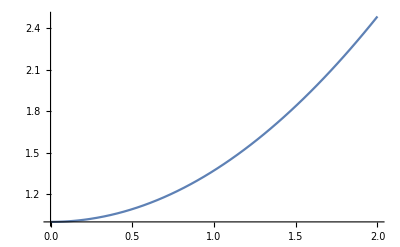

```mathematica
Λ=-1.1;
sol0=NDSolve[{16 r Λ a[r]^3-2 r^3 Λ a[r] (-1+a'[r]^2)+r^2 (-1+r^2 Λ) a'[r] (-1+a'[r]^2)+8 a[r]^2 (2 a'[r]+r (1-r^2 Λ) a''[r])==0,a[0.0001]==1,a'[0.00001]==0},{a[r]},{r,0,2}]//Quiet
Plot[{a[r]/.{sol0}},{r,0,2}]
```

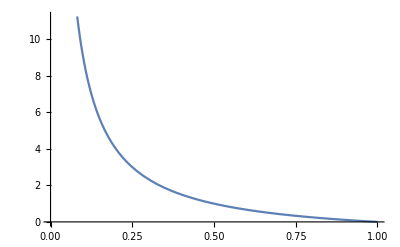

```mathematica
Plot[-(1-1/r),{r,0,1}]
```

## Gonzalo’s idea

```mathematica
eq1=(r*b[r]c[r](a'[r])^2-2r*a[r]b[r]c[r]a''[r]+r*a[r]c[r]a'[r]b'[r]-2r*a[r]b[r]a'[r]c'[r]-4a[r]b[r]c[r]a'[r])/(4r*(a[r])(b[r])^2 c[r]);
eq2=1/(4r*(a[r])^2(b[r])^2(c[r])^2)(r*b[r]*(c[r])^2-2r*a[r]b[r]*(c[r])^2 a''[r]+2r*(a[r])^2 b[r](c'[r])^2-4r(a[r])^2 b[r]c[r]c''[r]+b'[r](r*a[r](c[r])^2 a'[r]+4(a[r])^2(c[r])^2)+c'[r]*2(r(a[r])^2 c[r]b'[r]-4(a[r])^2 b[r]c[r]));
eq3=(2 r^2 a[r]b[r]c''[r]+2r*b[r]c[r]a'[r]-2r*a[r]c[r]b'[r]-4*a[r](b[r])^2+4a[r]b[r]c[r]+c'[r]*(r^2 b[r]a'[r]-r^2 a[r]b'[r]+8r*a[r]b[r]))/(4*r*r*a[r](b[r])^2 c[r]);
eq4=(2 r^2 a[r]b[r]c''[r]+2r*b[r]c[r]a'[r]-2r*a[r]c[r]b'[r]-4*a[r](b[r])^2+4a[r]b[r]c[r]+c'[r]*(r^2 b[r]a'[r]-r^2 a[r]b'[r]+8r*a[r]b[r]))/(4*r*r*a[r](b[r])^2 c[r]);
FullSimplify[eq1==0]
FullSimplify[eq2==0]
FullSimplify[eq3==0]
```

a'[r] (4/r-b'[r]/b[r]+(2 c'[r])/c[r])+2 a''[r]==a'[r]^2/a[r]

c[r]/a[r]+c[r] ((a'[r] b'[r])/b[r]-2 a''[r])+2 a[r] (-(4 c'[r])/r+c'[r]^2/c[r]+(b'[r] (2 c[r]+r c'[r]))/(r b[r])-2 c''[r])==0

(-(4 b[r])/r+(4 c[r])/r+8 c'[r]+(a'[r] (2 c[r]+r c'[r]))/a[r]-(b'[r] (2 c[r]+r c'[r]))/b[r]+2 r c''[r])/c[r]==0

```mathematica
FullSimplify[eq1+eq2+eq3+eq4==Λ]
```

2 r c[r] a''[r]+a[r] (b[r] (8/r+4 r Λ c[r])-(r c[r] a'[r] b'[r])/b[r]+(2 (c[r] (-2+r a'[r])-r c'[r]) (2 c[r]+r c'[r]))/(r c[r])+2 r c[r] a''[r])==(r c[r])/a[r]+(a'[r] (r c[r] b'[r]+b[r] (c[r] (4+r a'[r])+2 r c'[r])))/b[r]

```mathematica
FullSimplify[Solve[eq1+eq2+eq3+eq4==Λ,a''[r]]]
```

{{a''[r]→1/(2 r^2 a[r] (1+a[r]) b[r] c[r]^2)(r^2 b[r] c[r]^2+a[r]^2 (-4 b[r]^2 c[r] (2+r^2 Λ c[r])+r^2 c[r]^2 a'[r] b'[r]-2 b[r] (c[r] (-2+r a'[r])-r c'[r]) (2 c[r]+r c'[r]))+r a[r] c[r] a'[r] (r c[r] b'[r]+b[r] (c[r] (4+r a'[r])+2 r c'[r])))}}

```mathematica
a''[r]=1/(2 r^2 a[r] (1+a[r]) b[r] c[r]^2)(r^2 b[r] c[r]^2+a[r]^2 (-4 b[r]^2 c[r] (2+r^2 Λ c[r])+r^2 c[r]^2 a'[r] b'[r]-2 b[r] (c[r] (-2+r a'[r])-r c'[r]) (2 c[r]+r c'[r]))+r a[r] c[r] a'[r] (r c[r] b'[r]+b[r] (c[r] (4+r a'[r])+2 r c'[r])));
eq1=r*b[r]c[r](a'[r])^2-2r*a[r]b[r]c[r]a''[r]+r*a[r]c[r]a'[r]b'[r]-2r*a[r]b[r]a'[r]c'[r]-4a[r]b[r]c[r]a'[r]-4r*(a[r])^2(b[r])^2 c[r]*Λ;
eq2=r*b[r]*(c[r])^2-2r*a[r]b[r]*(c[r])^2 a''[r]+2r*(a[r])^2 b[r](c'[r])^2-4r(a[r])^2 b[r]c[r]c''[r]+b'[r](r*a[r](c[r])^2 a'[r]+4(a[r])^2(c[r])^2)+c'[r]*2(r(a[r])^2 c[r]b'[r]-4(a[r])^2 b[r]c[r])-4r*(a[r])^2(b[r])^2(c[r])^2*Λ;
eq3=2 r^2 a[r]b[r]c''[r]+2r*b[r]c[r]a'[r]-2r*a[r]c[r]b'[r]-4*a[r](b[r])^2+4a[r]b[r]c[r]+c'[r]*(r^2 b[r]a'[r]-r^2 a[r]b'[r]+8r*a[r]b[r])+4*r*r*a[r](b[r])^2 c[r]*Λ;
FullSimplify[eq1==0]
FullSimplify[eq2==0]
FullSimplify[eq3==0]
```

(b[r] (4 r^2 Λ a[r]^3 b[r] c[r]^2-r^2 c[r]^2 (-1+a'[r]^2)+4 r a[r] c[r] a'[r] (2 c[r]+r c'[r])+a[r]^2 (-8 b[r] c[r]+2 (2 c[r]+r c'[r])^2)))/(r (1+a[r]) c[r])==0

1/(r (1+a[r]))a[r] (-r b[r] c[r] (c[r] (-r+a'[r] (4+r a'[r]))+2 r a'[r] c'[r])+2 a[r] c[r] (4 b[r]^2+r b'[r] (2 c[r]+r c'[r])+b[r] (2 c[r] (-2+r a'[r])+r ((-8+r a'[r]) c'[r]-2 r c''[r])))+2 r a[r]^2 (-2 r Λ b[r]^2 c[r]^2+c[r] b'[r] (2 c[r]+r c'[r])+b[r] (r c'[r]^2-2 c[r] (2 c'[r]+r c''[r]))))==0

r b[r] a'[r] (2 c[r]+r c'[r])+a[r] (4 b[r]^2 (-1+r^2 Λ c[r])-r b'[r] (2 c[r]+r c'[r])+2 b[r] (2 c[r]+4 r c'[r]+r^2 c''[r]))==0

```mathematica
FullSimplify[Solve[eq3==0,c''[r]]]
```

{{c''[r]→(-r b[r] a'[r] (2 c[r]+r c'[r])+a[r] (b[r]^2 (4-4 r^2 Λ c[r])+r b'[r] (2 c[r]+r c'[r])-4 b[r] (c[r]+2 r c'[r])))/(2 r^2 a[r] b[r])}}

```mathematica
c''[r]=(-r b[r] a'[r] (2 c[r]+r c'[r])+a[r] (b[r]^2 (4-4 r^2 Λ c[r])+r b'[r] (2 c[r]+r c'[r])-4 b[r] (c[r]+2 r c'[r])))/(2 r^2 a[r] b[r]);
FullSimplify[eq1==0]
FullSimplify[eq2==0]
FullSimplify[eq3==0]
```

(b[r] (4 r^2 Λ a[r]^3 b[r] c[r]^2-r^2 c[r]^2 (-1+a'[r]^2)+4 r a[r] c[r] a'[r] (2 c[r]+r c'[r])+a[r]^2 (-8 b[r] c[r]+2 (2 c[r]+r c'[r])^2)))/(r (1+a[r]) c[r])==0

(a[r] b[r] (-r^2 c[r]^2 (-1+a'[r]^2)+4 r a[r] c[r] (2 r Λ b[r] c[r]+a'[r] (2 c[r]+r c'[r]))+2 a[r]^2 (2 b[r] c[r] (-2+r^2 Λ c[r])+(2 c[r]+r c'[r])^2)))/(r (1+a[r]))==0

True